# Different Stimulation pulses, 20mW,473nm

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141006 Mouse 8(Wavelenght pulsed)

```mathematica
samplingRate=1000./128
```

7.8125

```mathematica
gagFiles=FileNames["*.mat"]
```

{141006-01-200um-20mW,500ms,0'2Hz,40T,589nm.mat,141006-02-200um-20mW,2000ms,0'2Hz,40T,589nm(10ms-20Hz).mat,141006-03-200um-20mW,2000ms,0'2Hz,40T,589nm(10ms-10Hz).mat,141006-04-200um-20mW,2000ms,0'2Hz,40T,589nm(10ms-40Hz).mat,141006-05-200um-40mW,2000ms,0'2Hz,40T,589nm(10ms-20Hz).mat,141006-06-200um-40mW,2000ms,0'2Hz,40T,589nm(10ms-10Hz).mat,141006-07-200um-40mW,2000ms,0'2Hz,40T,589nm(10ms-40Hz).mat,141006-08-200um-20mW,500ms,0'2Hz,40T,473nm.mat,141006-09-200um-20mW,2000ms,0'2Hz,40T,473nm(10ms-20Hz).mat,141006-10-200um-20mW,2000ms,0'2Hz,40T,473nm(10ms-10Hz).mat,141006-11-200um-20mW,2000ms,0'2Hz,40T,473nm(10ms-40Hz).mat,141006-12-200um-40mW,2000ms,0'2Hz,40T,473nm(10ms-10Hz).mat,141006-13-200um-40mW,2000ms,0'2Hz,40T,473nm(10ms-20Hz).mat,141006-14-200um-40mW,2000ms,0'2Hz,40T,473nm(10ms-40Hz).mat,141006-15-200um-40mW,500ms,0'2Hz,40T,473nm.mat,141006-16-200um-40mW,500ms,0'2Hz,40T,589nm.mat}

## Functions

```mathematica
baselineNormalize[data_]:=Module[{},
(#-Mean[#[[1;;9]]])&/@data
];
```

```mathematica
meanBandPlot[data_, color_]:=Module[{means, sds},
means=Mean/@Transpose[data];
sds=StandardDeviation/@Transpose[data];
ListLinePlot[{means-sds, means+sds},
PlotStyle->None,
PlotRange->All,
Filling->{1->{{2},Opacity[1,color]}}
]
];
```

```mathematica
meanPlot[data_, color_,thick_, dataRange_:Automatic]:=
Module[{means,timePoints},
means=Mean/@Transpose[data];
If[dataRange===Automatic,
ListLinePlot[means,PlotStyle->{color,Thick}],
timePoints=Rescale[Range[Length[means]],{1,Length[means]},dataRange];
ListLinePlot[Transpose[{timePoints,means}],
PlotStyle->{color,Thickness[thick]},PlotRange->All]
]


];
```

```mathematica
means[data_]:=Module[{means, sds},
Mean/@Transpose[data]
];
```

```mathematica
trialPointPlot[data_, color_]:=Module[{},
ListPlot[data,PlotStyle->Opacity[0.2,color]]
];
```

```mathematica
gagColors= {Blue,Blue,Darker[Blue]}
```

{-Graphics-,-Graphics-,-Graphics-}

## Load Data

```mathematica
gagFitDataWave08=Map[Import,gagFiles];
Dimensions/@gagFitDataWave08
```

{{1,39,620},{1,39,620},{1,38,620},{1,39,620},{1,36,620},{1,39,620},{1,37,620},{1,39,620},{1,38,620},{1,38,620},{1,33,620},{1,37,620},{1,39,620},{1,39,620},{1,9,620},{1,39,620}}

```mathematica
gagFitDataWave08=Flatten[gagFitDataWave08,1];
Dimensions/@gagFitDataWave08
```

{{39,620},{39,620},{38,620},{39,620},{36,620},{39,620},{37,620},{39,620},{38,620},{38,620},{33,620},{37,620},{39,620},{39,620},{9,620},{39,620}}

```mathematica
(*Choose files for this condition*)
gagFitDataWave08= gagFitDataWave08[[{9,10,11}]];
Dimensions/@gagFitDataWave08
```

{{38,620},{38,620},{33,620}}

### Remove bad trials if necessary

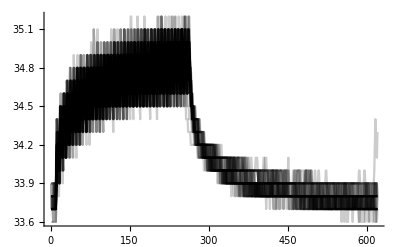
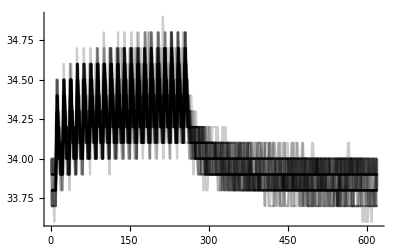
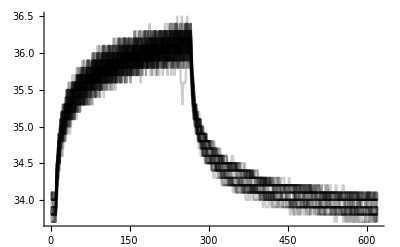

```mathematica
ListLinePlot[#,PlotStyle->Opacity[0.2,Black],PlotRange->All]&/@gagFitDataWave08
```

```mathematica
gagTemp=ListLinePlot[gagFitDataWave08[[2]],PlotStyle->Opacity[0.2,Black],PlotRange->All]
```

-Graphics-

```mathematica
Ordering[gagFitDataWave08[[2]][[;;, 1]],1]
```

{9}

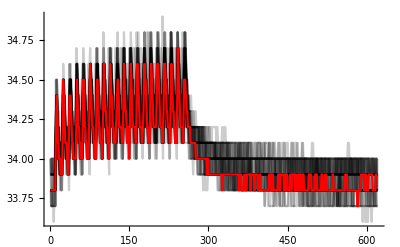

```mathematica
Show[gagTemp, ListLinePlot[gagFitDataWave08[[2]][[1]],PlotStyle->Red,PlotRange->All],PlotRange->All]
```

```mathematica
Dimensions/@gagFitDataWave08
```

{{38,620},{38,620},{33,620}}

```mathematica
(*gagFitDataWave08[[4]]=Delete [gagFitDataWave08[[4]],{{1},{3},{4},{11},{13}}];
Dimensions[gagFitDataWave08[[4]]]*)
```

```mathematica
(*gagFitDataWave08[[2]]=Delete [gagFitDataWave08[[2]],{{1}}];
Dimensions[gagFitDataWave08[[2]]]*)
```

```mathematica
(*gagFitDataWave08[[3]]=Delete [gagFitDataWave08[[3]],{{9}}];
Dimensions[gagFitDataWave08[[3]]]*)
```

## Normalize Data so Baseline is at 0, Set Range Variables

```mathematica
Dimensions/@gagFitDataWave08
```

{{38,620},{38,620},{33,620}}

```mathematica
gagFitDataWave08=baselineNormalize/@ gagFitDataWave08;
```

```mathematica
Dimensions/@gagFitDataWave08
```

{{38,620},{38,620},{33,620}}

```mathematica
2001/(1000/128.) (*figuring out stim duration*)
```

256.128

```mathematica
stimDuration=256;
stimStart=11;
stimEnd=stimStart+stimDuration-4;
fallStart=stimStart+stimDuration-1;
fallEnd=fallStart+200;
trialLength=Length[gagFitDataWave08[[1, 1]]]
```

620

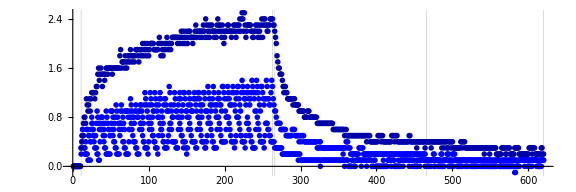

```mathematica
gagTempFitDataWave08=ListPlot[gagFitDataWave08[[All,1]],
GridLines->{{stimStart,stimEnd,fallStart,fallEnd,trialLength},None}, 
AspectRatio->1/3, ImageSize->72*8,PlotStyle->gagColors]
```

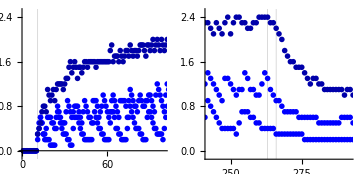

```mathematica
GraphicsRow[
{Show[gagTempFitDataWave08,PlotRange->{{0,100},All},AspectRatio->1],
Show[gagTempFitDataWave08,PlotRange->{stimStart+stimDuration+{-25,+25},All},AspectRatio->1]}, ImageSize->Medium]
```

## Cleaner Plots

```mathematica
Dimensions[Transpose[{gagFitDataWave08,gagColors}]]
```

{3,2}

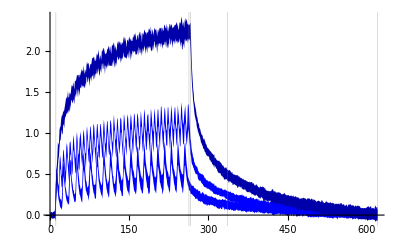

```mathematica
grSDWave08=Show[meanBandPlot[#[[1]],#[[2]]]& /@ Transpose[{gagFitDataWave08,gagColors}],
GridLines->{{stimStart,stimEnd,fallStart,trialLength,fallStart+70},None}, 
PlotRange->All]
```

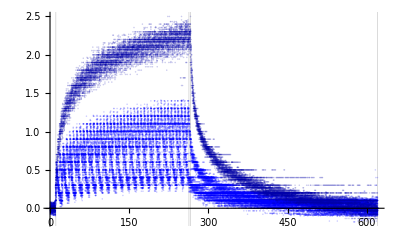

```mathematica
gagPointGraphWave08=Show[trialPointPlot[#[[1]],#[[2]]]& /@ Transpose[{gagFitDataWave08,gagColors}],
GridLines->{{stimStart,stimEnd,fallStart,trialLength},None}, 
PlotRange->All]
```

```mathematica
Options[ListLinePlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→True,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

```mathematica
gagThick={0.005,0.0025,0.0075};
```

```mathematica
gagDash={Medium,Small,Large};
```

```mathematica
gagLegend=LineLegend[{Directive[Opacity[0.65,Blue],Thickness[gagThick[[2]]]],Directive[Opacity[0.65,Blue],Thickness[gagThick[[1]]]],Directive[Opacity[0.65,Blue],Thickness[gagThick[[3]]]]},{"10 Hz","20 Hz","40 Hz"},LabelStyle->{FontFamily->"Helvetica",FontSize->8},LegendMarkerSize->{20,10},LegendLabel->Style["Pulse Frequency",Bold,FontSize->8]]
```

```mathematica
gagLegend2=LineLegend[{Directive[Opacity[1,Black],Dashing[gagDash[[2]]]],Directive[Opacity[1,Black],Dashing[gagDash[[1]]]],Directive[Opacity[1,Black],Dashing[gagDash[[3]]]]},{"10 %","20 %","40 %"},LabelStyle->{FontFamily->"Helvetica",FontSize->8},LegendMarkerSize->{20,10},LegendLabel->Style["Model Prediction",Bold,FontSize->8]]
```

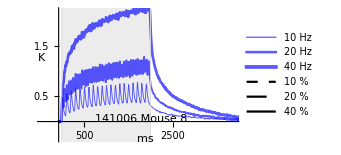

```mathematica
grMeanWave08=Show[meanPlot[#[[1]],Opacity[0.65,Blue],#[[2]],{-11,620-11}*samplingRate]& /@ Transpose[{gagFitDataWave08,gagThick}],ImageSize->72*3.5,
GridLines->{{stimStart-12,stimEnd-11+4}*samplingRate,None},GridLinesStyle->Thickness[0.0025],PlotRange->{{-60,500}*samplingRate,{-0.35,2.2}},AspectRatio->1/GoldenRatio, AxesLabel->{None, None},Ticks->{Table[n,{n,500,3500,1000}],{0.5,1,1.5,2}},TicksStyle->Directive[Black,9],
AxesStyle->Thickness[0.004], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{-10*samplingRate,0},LabelStyle->{FontSize->12,FontWeight->"Bold"},
Prolog->{Opacity[0.15,Gray], Rectangle[{(stimStart-12)*samplingRate,-1},{(stimEnd-11+4)*samplingRate,7}]},
Epilog->{Text["ms",{240*samplingRate,-0.35},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Text["K",{-60*samplingRate,1.25},BaseStyle->{FontSize->9,FontWeight->"Bold"}],
Inset[gagLegend,{425*samplingRate,1.7}],Inset[gagLegend2,{425*samplingRate,0.65}],Text["141006 Mouse 8",{230*samplingRate,0.05},BaseStyle->{FontSize->2}]}]
```

```mathematica
shiftRBlue20=3.814287284855608*^-9;
```

```mathematica
funcRBlue20=1.0292278193479125 Log[0.9999999965609866+0.9016136306865709 #1]&
```

1.02923 Log[1.+0.901614 #1]&

```mathematica
fRiseBlue20[fr_]:= Evaluate[funcRBlue20[fr-shiftRBlue20]];
```

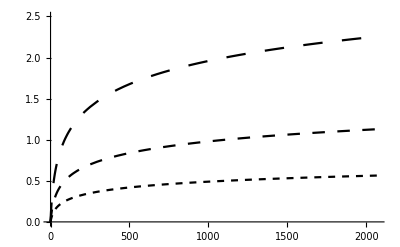

```mathematica
grRPlot= Plot[{0.2*fRiseBlue20[x/samplingRate],0.1*fRiseBlue20[x/samplingRate],0.4*fRiseBlue20[x/samplingRate]},{x,0,(stimEnd+2)*samplingRate}, PlotStyle->{{Black,Dashing[gagDash[[1]]]},{Black,Dashing[gagDash[[2]]]},{Black,Dashing[gagDash[[3]]]}},PlotRange->{All,{0,2.5}}]
```

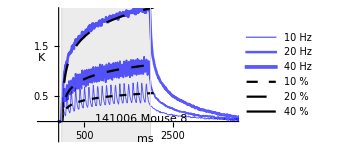

```mathematica
gagDutyCycleGraph=Show[grMeanWave08,grRPlot]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141006 Mouse 8(Wavelenght pulsed)

```mathematica
Export["141006.PulseFitting(20mW,473nm).png",gagDutyCycleGraph,ImageResolution->600]
```

141006.PulseFitting(20mW,473nm).png

```mathematica
Export["141006.PulseFitting(20mW,473nm).pdf",gagDutyCycleGraph,ImageResolution->600]
```

141006.PulseFitting(20mW,473nm).pdf